Measuring the boiling point of the vacuum of quantum electrodynamics

Anthony Hartin, Andreas Ringwald, and Natalia Tapia, Phys Rev D 99, 036008 (2019)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

## Figure 2: dimensionless function Fγ(ξ,χ)

This computation might take a long time...

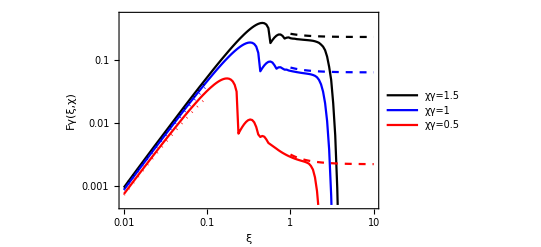

```mathematica
Clear[α,me,Ee,EeGeV,χ,X,X0,ΓBPPP14,θ,ξ,e,Fγ8,Fγ9,Fγ,n,n0,vn,zv]

(* eq 6 *)
Fγ[ξ_,χ_]:=Module[{vn,zv,n0,n,v},
(* eq 7 aux functions *)
n0=(2ξ(1+ξ^2))/χ;
vn=(χ n)/(2ξ(1+ξ^2));
zv=(4 ξ^2 Sqrt[1+ξ^2])/χ(v(vn-v))^(1/2);
Return[Sum[NIntegrate[(2 BesselJ[n,zv]^2+ξ^2(2v-1)(BesselJ[n+1,zv]^2+BesselJ[n-1,zv]^2-2 BesselJ[n,zv]^2))/(v Sqrt[v(v-1)]),{v,1,vn},AccuracyGoal->Infinity],{n,Ceiling[n0],Ceiling[n0]+40,1}]]
]

(* eq8 ξ<<1 *)
Fγ8=2 ξ^2(Log[(2χ)/ξ]-1);
(* eq9 ξ>>1 *)
Fγ9=
3/4 Sqrt[3/2]χ Exp[-8/(3χ)(1-1/(15 ξ^2))];

(* plot *)
Show[{LogLogPlot[{Fγ[ξ,1.5],Fγ[ξ,1],Fγ[ξ,0.5]},{ξ,10^-2,10^1},PlotStyle->{{Black},{Blue},{Red}},PlotRange->{{10^-2,10^1},{5 10^-4,5 10^-1}},Frame->True,FrameLabel->{"ξ","Fγ(ξ,χ)"},PlotPoints->3,PlotLegends->{"χγ=1.5","χγ=1","χγ=0.5"}],LogLogPlot[{Fγ8/.{χ->1.5},Fγ8/.{χ->1},Fγ8/.{χ->0.5}},{ξ,10^-2,10^-1},PlotStyle->{{Black,Dotted},{Blue,Dotted},{Red,Dotted}}],LogLogPlot[{Fγ9/.{χ->1.5},Fγ9/.{χ->1},Fγ9/.{χ->0.5}},{ξ,10^0,10^1},PlotStyle->{{Black,Dashed},{Blue,Dashed},{Red,Dashed}}]}]
```

## Figure 5

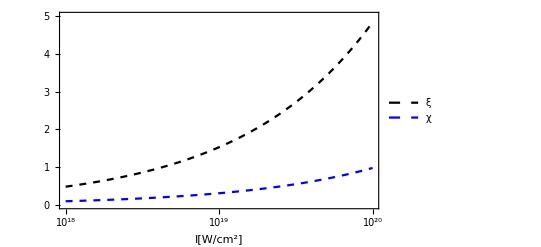

```mathematica
Clear[α,me,Ee,EeGeV,χ,X,X0,ΓBPPP14,θ,ξ,e,Ι]
(* "circularly polarized infinite plane wave (IPW)", before equation 6 *)

(* a0 of CP laser and 0.8 μm optical laser*)
ξ=0.855 Sqrt[Ι/10^18]0.8/√2 ;
(* equation 16 *)
χ=0.1576(1+Cos[θ])EeGeV/17.5(Ι/10^19)^(1/2);(*[]*)
(* parameters *)
EeGeV=17.5;(*[GeV]*)
θ=π/12;(*[]*)

LogLinearPlot[{ξ,χ},{Ι,10^18,10^20},PlotRange->{0,5},Frame->True,FrameLabel->{"I[W/cm^2]",""},PlotLegends->{"ξ","χ"},PlotStyle->{{Dashed,Black},{Dashed,Blue}}]
```

## Figure 6

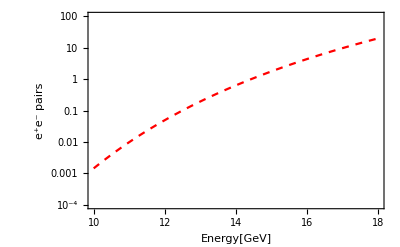

```mathematica
Clear[α,me,Ee,EeGeV,χ,X,X0,ΓBPPP14,θ,ξ,e]
(* equation 14 *)
ΓBPPP14=(α me^2)/Ee 9/128 Sqrt[3/2] χ^2 Exp[-8/(3χ)(1-1/(15 ξ^2))] X/X0;
(* equation 16 *)
χ=0.1576(1+Cos[θ])EeGeV/17.5(Ι/10^19)^(1/2);
θ=π/12;(*[]*)

(* parameters *)
e=1.6 10^-19;(*[C]*)
me=9.1 10^-31;(*[Kg]*)
α=1/137;(*[]*)

Ι=5 10^18;(*[W/cm^2]*)
X=0.01 X0;(*[]*)
(*λ=0.8;*)
ξ=0.855 Sqrt[Ι/10^18]0.8/√2 ;
Ne=6 10^9;(*[] number of electrons of energy Ee *)

LogPlot[{10^54.4 Ne ΓBPPP14/.{Ee->10^9 e EeGeV}},{EeGeV,10,18},PlotStyle->{{Red,Dashed}},Frame->True,FrameLabel->{"Energy[GeV]","e^+e^- pairs"},PlotRange->{10^-4,10^2}]
```